```mathematica
(* Lets try this test -- integration of a Gaussian using Newton-Cotes rules *)
f[x_]=(Sin[x]^2+x^2+2 x^4+1/10)Exp[-x^2];
xmax=7;
xmin=-xmax;
exact=Re[Integrate[f[x],{x,xmin,xmax}]];
Δ = (xmax-xmin)/(nOfPoints-1);

rectangularLeft=Table[{nOfPoints,Δ Sum[f[xmin+Δ (i-1)],{i,1,nOfPoints-1}]},{nOfPoints,10,100,2}];
rectangularRight=Table[{nOfPoints,Δ Sum[f[xmin+Δ (i-1)],{i,2,nOfPoints}]},{nOfPoints,10,100,2}];
trapezoidal=Table[{nOfPoints,(f[xmin]+f[xmax])/2 Δ+Δ Sum[f[xmin+Δ (i-1)],{i,2,nOfPoints-1}]},{nOfPoints,10,100,2}];
simpsonsOneThird=Table[{nOfPoints,Δ/3(f[xmin]+f[xmax]+ Sum[If[EvenQ[i-1],2,4]f[xmin+Δ (i-1)],{i,2,nOfPoints-1}])},{nOfPoints,11,100,2}];
simpsonsThreeThirds=Table[{nOfPoints,(3Δ)/8(f[xmin]+f[xmax]+ Sum[If[Mod[i-1,3]==0,2,3]f[xmin+Δ (i-1)],{i,2,nOfPoints-1}])},{nOfPoints,10,100,3}];
N[N[rectangularLeft,20]];
N[N[rectangularRight,20]];
N[N[trapezoidal,20]];
N[N[simpsonsOneThird,20]];
Clear[nOfPoints,array,Δ,xmin,xmax]
rule={x_,y_}->{x,Abs[y-exact]};
rectangularLeftErrors=N[N[rectangularLeft/.rule,20]];
rectangularRightErrors=N[N[rectangularRight/.rule,20]];
trapezoidalErrors=N[N[trapezoidal/.rule,20]];
simpsonsOneThirdErrors=N[N[simpsonsOneThird/.rule,20]];
simpsonsThreeThirdsErrors=N[N[simpsonsThreeThirds/.rule,20]];
Fit[Log[Take[rectangularLeftErrors,-20]],{1,x},x];
Fit[Log[Take[rectangularRightErrors,-20]],{1,x},x];
Fit[Log[Take[trapezoidalErrors,-20]],{1,x},x]
Fit[Log[Take[simpsonsOneThirdErrors,-20]],{1,x},x]
Fit[Log[Take[simpsonsThreeThirdsErrors,-20]],{1,x},x]
```

-35.0995-1.86116 x

25.01-15.676 x

156.912-42.3457 x

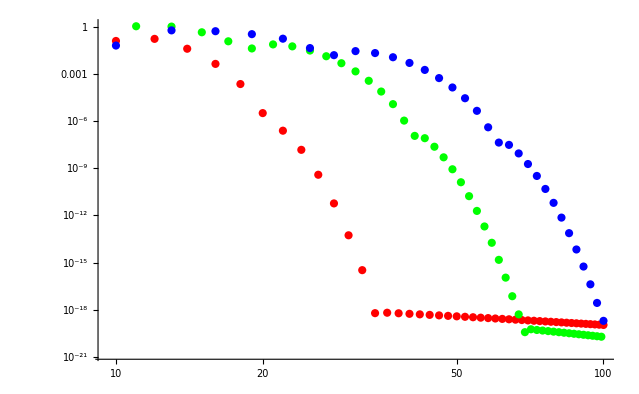

```mathematica
ListLogLogPlot[{trapezoidalErrors,simpsonsOneThirdErrors,simpsonsThreeThirdsErrors},PlotStyle->{Red,Green,Blue}]
```

```mathematica
Clear[f]
```

```mathematica
nOfPoints=7;
Δ=(xmax-xmin)/(nOfPoints-1);
(3Δ)/8(f[xmin]+f[xmax]+ Sum[If[Mod[i-1,3]==0,2,3]f[xmin+Δ (i-1)],{i,2,nOfPoints-1}])
n=nOfPoints-1;
Clear[nOfPoints,n,f]
```

1/16 (xmax-xmin) (f[xmax]+f[xmin]+3 f[(xmax-xmin)/6+xmin]+3 f[(xmax-xmin)/3+xmin]+2 f[(xmax-xmin)/2+xmin]+3 f[(2 (xmax-xmin))/3+xmin]+3 f[(5 (xmax-xmin))/6+xmin])